# Stellar Evolution Simulator Reese Danzer & Karthik Boyareddygari

## Output:

```mathematica
interface[1]
```

First::normal: Nonatomic expression expected at position 1 in First[Automatic].

## Main Code:

```mathematica
datalist=initialize["One Solar Mass.txt"];
data=datalist[[1]];
oneMSunData=datalist[[2]];
```

```mathematica
interface[solarMass_]:=
DynamicModule[{
maxStep=Length[oneMSunData],
maxRadius=Max[data["Radius"]],
maxLuminosity=Max[data["Luminosity"]],
maxTSurface=Max[data["T_s"]],
color,radius,surfaceTemp,centerTemp,luminosity,stepFunction
},
Manipulate[
color=radiusFunction[age]^-1;
radius=radiusFunction[age];
luminosity=luminosityFunction[age];
surfaceTemp=surfaceTempFunction[age];
centerTemp=centerTempFunction[age];
(*This will be the list of changing variables to be used below, because if we just slap the commands in themselves it will get really cluttered really fast.*)
GraphicsGrid[{
{Graphics3D[{Hue[color],Tooltip[Sphere[{0,0,0} ,radius]]},Background->Black,Boxed->False,PlotRange->maxRadius],
(*The Sphere Graphic*)
Panel[Show[ListLogPlot[Tooltip[{{surfaceTemp,luminosity}}],PlotStyle->Directive[Yellow,Thick],PlotRange->{{maxTSurface,0},{0,maxLuminosity}},Axes->True,GridLines->Automatic, Background->Black,AxesStyle->Directive[Red],AxesLabel->{"T_s","L⊙"}]],Background->Black]},
(*The HR Diagram*)
{Graphics[{Hue[0.02],Tooltip[Disk[{0,0},1]],Hue[0.15],Tooltip[Disk[{0,0},1/age]]},PlotRange->1.1,Background->Darker[Gray,0.75]],
(*The Internal Diagram*)
Panel[Graphics[{FontSize->16, Text[
"Surface Temperature: "<>ToString[NumberForm[Round[surfaceTemp],DigitBlock->3]]<>"°K"<>
"\nCenter Tempurature: "<>ToString[NumberForm[Round[centerTemp],DigitBlock->3]]<>"°K"<>"\nRadius: "<>ToString[NumberForm[radius,DigitBlock->3,NumberSeparator->","]]<>" R⊙"<>
"\nLuminosity: "<>ToString[NumberForm[luminosity,DigitBlock->3,NumberSeparator->","]]<>" L⊙"<>
"\nAge: "<>ToString[AccountingForm[age,DigitBlock->3,NumberSeparator->","]]<>" Years"]}]]}
(*The Text Readouts*)
},
ContentSelectable->False,
(*So they don't get their grubby hands on our nice animation.*)
ImageSize->Full
],
{{age,1,"Age"},Dynamic[min],maxAge},{{min,1,"Minimum Age"},1},ContentSize->{600,600}]
]
```

## Data Initialization Function

```mathematica
initialize[fileName_]:=
Module[{association,data},
SetDirectory[NotebookDirectory[]];
data=Import[fileName,"Table"];
Return[
{<|"Age"->data[[All,2]],"Mass"->data[[All,3]],"Luminosity"->10^data[[All,4]],"Radius"->10^data[[All,5]],"T_s"->10^data[[All,6]],"T_c"->10^data[[All,7]],"ρ_c"->10^data[[All,8]],"P_c"->10^data[[All,9]],"R_He"->data[[All,27]],"R_C"->data[[All,28]],"R_O"->data[[All,29]]|>,data}
];
]
```

## Connect

```mathematica
connect[listoflist_]:=(*assume that all lists in listoflist are of the same length because we are inputting them*)
Module[{length=Length[listoflist[[1]]],lengthmain=Length[listoflist],final},
final=Table[listoflist[[k,i]],{i,1,length},{k,1,lengthmain}];(*create a list of length lists each being lengthmain elements long*)
Return[final]
]
```

## Datasets:

```mathematica
Dynamic[data]
```

## Variable Explanations:

Age: A number from 0 to 1 that represents the position the data point represents in the star’s life.
Mass: Mass of the star in M⊙.
Radius: Radius of the star, in R⊙.
Luminosity: Luminosity of the star, in L⊙.

## Data Visualizations:

## One Msun:

#### Age vs. Step (maxAge Initialization)

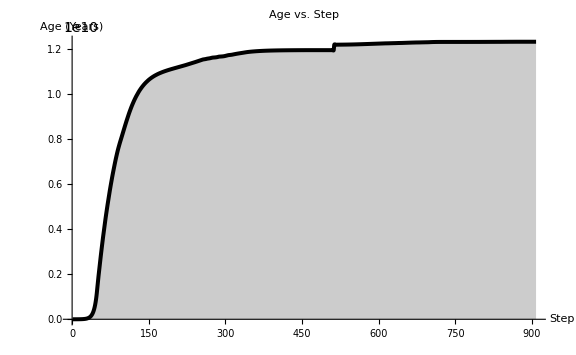

```mathematica
maxAge=Max[data["Age"]];
Show[Plot[Interpolation[Normal[data["Age"]]][x],{x,1,908},PlotRange->Full,PlotStyle->Directive[Black,Thickness[0.005]],Filling->Bottom,AxesLabel->{"Step","Age (Years)"},PlotLabel->"Age vs. Step",AxesStyle->Directive[Black,Thick]],ImageSize->Large]
```

#### Mass

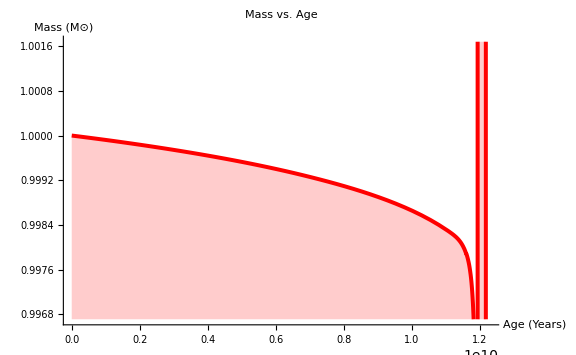

```mathematica
massCoordList=DeleteDuplicatesBy[connect[{data["Age"],data["Mass"]}],First];
massFunction=Interpolation[massCoordList];
Show[{Plot[massFunction[x],{x,0,maxAge},
PlotStyle->Directive[Red,Thickness[0.005]],Filling->Bottom,AxesLabel->{"Age (Years)","Mass (M⊙)"},PlotLabel->"Mass vs. Age",AxesStyle->Directive[Black,Thick]]},ImageSize->Large]
```

#### Radius

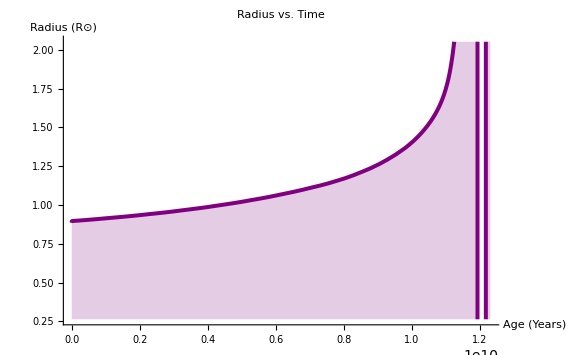

```mathematica
radiusCoordList=DeleteDuplicatesBy[connect[{data["Age"],data["Radius"]}],First];
radiusFunction=Interpolation[radiusCoordList];
Show[{Plot[radiusFunction[x],{x,0,maxAge},
PlotStyle->Directive[Purple,Thickness[0.005]],Filling->Bottom,AxesLabel->{"Age (Years)","Radius (R⊙)"},PlotLabel->"Radius vs. Time",AxesStyle->Directive[Black,Thick]]},ImageSize->Large]
```

```mathematica
Max[data["Radius"]]
```

275.892

```mathematica
FindMaximum[radiusFunction[x],{x,1*10^9}]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.7533,{x→1.1×10^10}}

```mathematica
Position[data["Radius"],275.89231287562427]
```

{{871}}

#### Luminosity

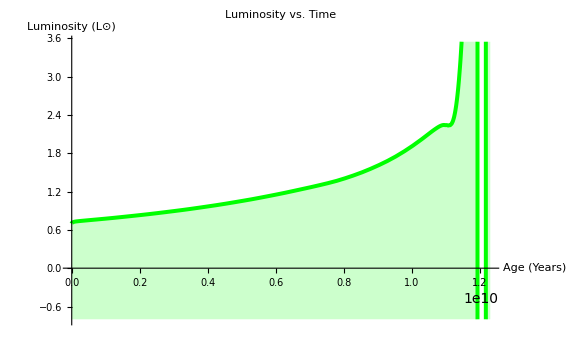

```mathematica
luminosityCoordList=DeleteDuplicatesBy[connect[{data["Age"],data["Luminosity"]}],First];
luminosityFunction=Interpolation[luminosityCoordList];
Show[{Plot[luminosityFunction[x],{x,0,maxAge},
PlotStyle->Directive[Green,Thickness[0.005]],Filling->Bottom,AxesLabel->{"Age (Years)","Luminosity (L⊙)"},PlotLabel->"Luminosity vs. Time",AxesStyle->Directive[Black,Thick]]},ImageSize->Large]
```

#### Surface Tempurature

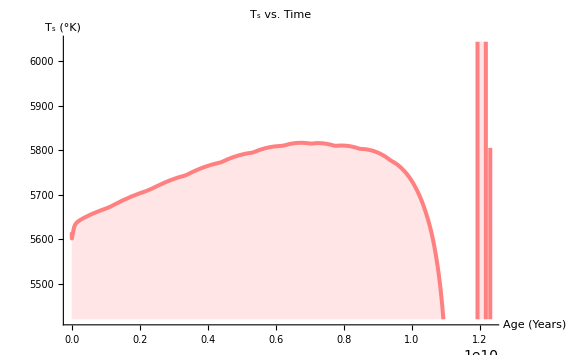

```mathematica
surfaceTempCoordList=DeleteDuplicatesBy[connect[{data["Age"],data["T_s"]}],First];
surfaceTempFunction=Interpolation[surfaceTempCoordList];
Show[{Plot[surfaceTempFunction[x],{x,0,maxAge},
PlotStyle->Directive[Pink,Thickness[0.005]],Filling->Bottom,AxesLabel->{"Age (Years)","T_s (°K)"},PlotLabel->"T_s vs. Time",AxesStyle->Directive[Black,Thick]]},ImageSize->Large]
```

#### Center Tempurature

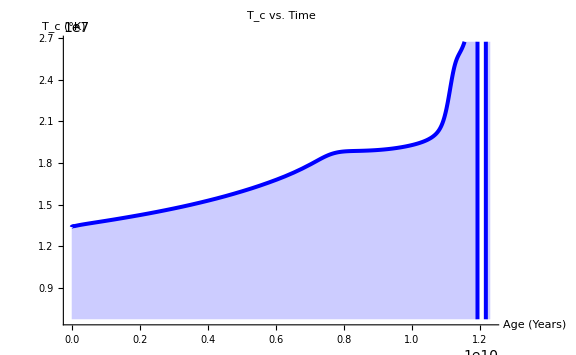

```mathematica
centerTempCoordList=DeleteDuplicatesBy[connect[{data["Age"],data["T_c"]}],First];
centerTempFunction=Interpolation[centerTempCoordList];
Show[{Plot[centerTempFunction[x],{x,0,maxAge},
PlotStyle->Directive[Blue,Thickness[0.005]],Filling->Bottom,AxesLabel->{"Age (Years)","T_c (°K)"},PlotLabel->"T_c vs. Time",AxesStyle->Directive[Black,Thick]]},ImageSize->Large]
```

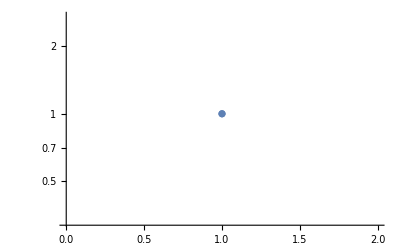

```mathematica
ListLogPlot[{{1,1}}]
```